```mathematica
$Assumptions ={ao>0,a[_]>0,ko>0,k[_]>0,c[_]>0,co>0, n ∈ Integers};

ψo = fo[n] BesselJ[n,ko r];
ψ[s] = Ao[n]HankelH1[n,ko r];
ψ[0] = f[0,n] BesselJ[n,k[0] r];
ψ[1] = f[1,n] BesselJ[n,k[1] r] + A[1,n]HankelH1[n,k[1] r];


eqs = {ψ[1]  == ψ[0]/.r-> a[0],D[ψ[1],r]/ρ[1]  == D[ψ[0],r]/ρ[0]/.r-> a[0], ψ[s] + ψo  == ψ[1]/.r-> a[1],D[ψ[1],r]/ρ[1]  == D[ψ[s] + ψo ,r]/ρo/.r-> a[1]};

Ao[n]/.Solve[eqs,{Ao[n],f[0,n],f[1,n],A[1,n]}] /.{ρo -> qo ko,ρ[1] -> q[1] k[1],ρ[0] -> q[0] k[0]} //Simplify
```

{(fo[n] (qo BesselJ[n,ko a[1]] ((BesselJ[-1+n,a[1] k[1]]-BesselJ[1+n,a[1] k[1]]) HankelH1[n,a[1] k[1]]-BesselJ[n,a[1] k[1]] (HankelH1[-1+n,a[1] k[1]]-HankelH1[1+n,a[1] k[1]])) (BesselJ[n,a[0] k[0]] (HankelH1[-1+n,a[0] k[1]]-HankelH1[1+n,a[0] k[1]]) q[0]-(BesselJ[-1+n,a[0] k[0]]-BesselJ[1+n,a[0] k[0]]) HankelH1[n,a[0] k[1]] q[1])-(qo BesselJ[n,ko a[1]] (HankelH1[-1+n,a[1] k[1]]-HankelH1[1+n,a[1] k[1]])-(BesselJ[-1+n,ko a[1]]-BesselJ[1+n,ko a[1]]) HankelH1[n,a[1] k[1]] q[1]) (HankelH1[n,a[1] k[1]] (BesselJ[n,a[0] k[0]] (BesselJ[-1+n,a[0] k[1]]-BesselJ[1+n,a[0] k[1]]) q[0]-BesselJ[n,a[0] k[1]] (BesselJ[-1+n,a[0] k[0]]-BesselJ[1+n,a[0] k[0]]) q[1])-BesselJ[n,a[1] k[1]] (BesselJ[n,a[0] k[0]] (HankelH1[-1+n,a[0] k[1]]-HankelH1[1+n,a[0] k[1]]) q[0]-(BesselJ[-1+n,a[0] k[0]]-BesselJ[1+n,a[0] k[0]]) HankelH1[n,a[0] k[1]] q[1]))))/(-qo HankelH1[n,ko a[1]] ((BesselJ[-1+n,a[1] k[1]]-BesselJ[1+n,a[1] k[1]]) HankelH1[n,a[1] k[1]]-BesselJ[n,a[1] k[1]] (HankelH1[-1+n,a[1] k[1]]-HankelH1[1+n,a[1] k[1]])) (BesselJ[n,a[0] k[0]] (HankelH1[-1+n,a[0] k[1]]-HankelH1[1+n,a[0] k[1]]) q[0]-(BesselJ[-1+n,a[0] k[0]]-BesselJ[1+n,a[0] k[0]]) HankelH1[n,a[0] k[1]] q[1])+(qo HankelH1[n,ko a[1]] (HankelH1[-1+n,a[1] k[1]]-HankelH1[1+n,a[1] k[1]])-HankelH1[n,a[1] k[1]] (HankelH1[-1+n,ko a[1]]-HankelH1[1+n,ko a[1]]) q[1]) (HankelH1[n,a[1] k[1]] (BesselJ[n,a[0] k[0]] (BesselJ[-1+n,a[0] k[1]]-BesselJ[1+n,a[0] k[1]]) q[0]-BesselJ[n,a[0] k[1]] (BesselJ[-1+n,a[0] k[0]]-BesselJ[1+n,a[0] k[0]]) q[1])-BesselJ[n,a[1] k[1]] (BesselJ[n,a[0] k[0]] (HankelH1[-1+n,a[0] k[1]]-HankelH1[1+n,a[0] k[1]]) q[0]-(BesselJ[-1+n,a[0] k[0]]-BesselJ[1+n,a[0] k[0]]) HankelH1[n,a[0] k[1]] q[1])))}

```mathematica
ClearAll[ψo,ψ,J,H]
ψo = fo[n] Subscript[J, n][ko r];
ψ[s] = Ao[n]Subscript[H, n][ko r];
ψ[0] = f[0,n] Subscript[J, n][k[0] r];
ψ[1] = f[1,n] Subscript[J, n][k[1] r] + A[1,n]Subscript[H, n][k[1] r];
eqs = {ψ[1]  == ψ[0]/.r-> a[0],D[ψ[1],r]/ρ[1]  == D[ψ[0],r]/ρ[0]/.r-> a[0], ψ[s] + ψo  == ψ[1]/.r-> a[1],D[ψ[1],r]/ρ[1]  == D[ψ[s] + ψo ,r]/ρo/.r-> a[1]};
Ao[n]/.Solve[eqs,{Ao[n],f[0,n],f[1,n],A[1,n]}] /.{ρo -> qo ko,ρ[1] -> q[1] k[1],ρ[0] -> q[0] k[0]} ;
tmp = Apart@FullSimplify[%[[1]]/.{Inactive[BesselJ]:> J,Inactive[HankelH1]:> H, a[n_]:> Subscript[a, n], q[n_]:> Subscript[q, n], k[n_]:> Subscript[k, n]}];
```

```mathematica
tmp == fo[n]/(Subscript[H, n][ko Subscript[a, 1]])(-Subscript[J, n][ko Subscript[a, 1]]+Subscript[q, 1]((Subscript[J, n][ko Subscript[a, 1]] Subscript[H, n]'[ko Subscript[a, 1]]- Subscript[J, n]'[ko Subscript[a, 1]]Subscript[H, n][ko Subscript[a, 1]]) (Subscript[q, 1] (Subscript[H, n][Subscript[a, 1] Subscript[k, 1]] Subscript[J, n][Subscript[a, 0] Subscript[k, 1]]-Subscript[H, n][Subscript[a, 0] Subscript[k, 1]] Subscript[J, n][Subscript[a, 1] Subscript[k, 1]]) Subscript[J, n]'[Subscript[a, 0] Subscript[k, 0]]+Subscript[q, 0] Subscript[J, n][Subscript[a, 0] Subscript[k, 0]] (Subscript[J, n][Subscript[a, 1] Subscript[k, 1]] Subscript[H, n]'[Subscript[a, 0] Subscript[k, 1]]-Subscript[H, n][Subscript[a, 1] Subscript[k, 1]] Subscript[J, n]'[Subscript[a, 0] Subscript[k, 1]])) )/(Subscript[q, 1] Subscript[J, n]'[Subscript[a, 0] Subscript[k, 0]] (Subscript[q, 1] Subscript[H, n]'[ko Subscript[a, 1]](Subscript[H, n][Subscript[a, 1] Subscript[k, 1]] Subscript[J, n][Subscript[a, 0] Subscript[k, 1]]-Subscript[H, n][Subscript[a, 0] Subscript[k, 1]] Subscript[J, n][Subscript[a, 1] Subscript[k, 1]]) +qo Subscript[H, n][ko Subscript[a, 1]] (Subscript[H, n][Subscript[a, 0] Subscript[k, 1]] Subscript[J, n]'[Subscript[a, 1] Subscript[k, 1]]-Subscript[J, n][Subscript[a, 0] Subscript[k, 1]] Subscript[H, n]'[Subscript[a, 1] Subscript[k, 1]]))+Subscript[q, 0] Subscript[J, n][Subscript[a, 0] Subscript[k, 0]] (Subscript[q, 1] Subscript[H, n]'[ko Subscript[a, 1]] (Subscript[J, n][Subscript[a, 1] Subscript[k, 1]] Subscript[H, n]'[Subscript[a, 0] Subscript[k, 1]]-Subscript[H, n][Subscript[a, 1] Subscript[k, 1]] Subscript[J, n]'[Subscript[a, 0] Subscript[k, 1]])+qo Subscript[H, n][ko Subscript[a, 1]] (Subscript[H, n]'[Subscript[a, 1] Subscript[k, 1]] Subscript[J, n]'[Subscript[a, 0] Subscript[k, 1]]-Subscript[H, n]'[Subscript[a, 0] Subscript[k, 1]] Subscript[J, n]'[Subscript[a, 1] Subscript[k, 1]]))))//Simplify
```

True

```mathematica
F[f_,g_][x_,y_]:= f[x] g[y]-f[y] g[x]
Fd[f_,g_][x_,y_]:= f[x] g'[y]-f'[y] g[x]


Yd[x_,y_]=  Fd[Subscript[H, n],Subscript[J, n]] [x,y];
Y[x_,y_]=  F[Subscript[H, n],Subscript[J, n]] [x,y];
Ydd[x_,y_]=  F[Subscript[H, n]',Subscript[J, n]'] [x,y];
ClearAll[q]
dq = qo/Subscript[q, 1];
dq0 = Subscript[q, 0]/Subscript[q, 1];
 dq/.{qo -> ρo co, Subscript[q, 1]-> Subscript[ρ, 1] Subscript[c, 1] , Subscript[q, 0]-> Subscript[ρ, 0] Subscript[c, 0]}
dq0/.{qo -> ρo co, Subscript[q, 1]-> Subscript[ρ, 1] Subscript[c, 1] , Subscript[q, 0]-> Subscript[ρ, 0] Subscript[c, 0]}

tmp == -fo[n](Subscript[J, n][ko Subscript[a, 1]])/(Subscript[H, n][ko Subscript[a, 1]])-fo[n](Yd [ko Subscript[a, 1],ko Subscript[a, 1]])/(Subscript[H, n][ko Subscript[a, 1]]) (  Y [Subscript[a, 1] Subscript[k, 1],Subscript[a, 0] Subscript[k, 1]] Subscript[J, n]'[Subscript[a, 0] Subscript[k, 0]]-dq0 Subscript[J, n][Subscript[a, 0] Subscript[k, 0]] Yd [Subscript[a, 1] Subscript[k, 1],Subscript[a, 0] Subscript[k, 1]] )/( Subscript[J, n]'[Subscript[a, 0] Subscript[k, 0]] (dq Subscript[H, n][ko Subscript[a, 1]] Yd [Subscript[a, 0] Subscript[k, 1],Subscript[a, 1] Subscript[k, 1]]+ Subscript[H, n]'[ko Subscript[a, 1]]Y[Subscript[a, 1] Subscript[k, 1],Subscript[a, 0] Subscript[k, 1]])+dq0 Subscript[J, n][Subscript[a, 0] Subscript[k, 0]] (dq Subscript[H, n][ko Subscript[a, 1]]Ydd [Subscript[a, 1] Subscript[k, 1],Subscript[a, 0] Subscript[k, 1]]- Subscript[H, n]'[ko Subscript[a, 1]] Yd[Subscript[a, 1] Subscript[k, 1],Subscript[a, 0] Subscript[k, 1]])) //Simplify
```

(co ρo)/(c_1 ρ_1)

(c_0 ρ_0)/(c_1 ρ_1)

True

```mathematica
D[Y[x,y],x,y]

Yd [y,x]+Yd [x,y]//Simplify
```

-H_n'[y] J_n'[x]+H_n'[x] J_n'[y]

-J_n[y] H_n'[x]-J_n[x] H_n'[y]+H_n[y] J_n'[x]+H_n[x] J_n'[y]

## Addition Theorems

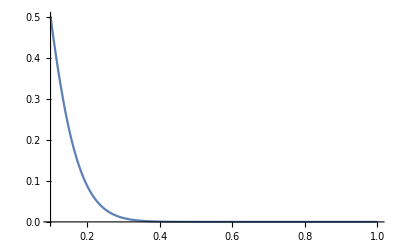

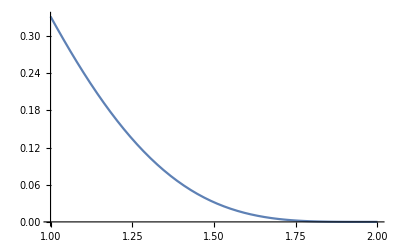

```mathematica
ClearAll[Graf,R,Θ]
R[l_] := Norm[{x,y}-{x[l],y[l]}];
Θ[l_] := ArcTan@@({x,y}-{x[l],y[l]});
R[l_,j_] := Norm[{x[j],y[j]}-{x[l],y[l]}];
Θ[l_,j_] := ArcTan@@({x[j],y[j]}-{x[l],y[l]});

Graf[H_,M_]:= H[n,R[l]] ⅇ^(ⅈ n Θ[l])  - Sum[H[n-m,R[l,j]] ⅇ^(ⅈ (n-m) Θ[l,j])BesselJ[m, R[j]] ⅇ^(ⅈ m Θ[j]),{m,-M,M}];
error =Abs[ Graf[HankelH1,50]/HankelH1[n,R[l]]]/.{x[l]-> 0,y[l]-> 0, x[j]-> 2,y[j]-> 0, y->0};
Plot[error/.{n->3},{x,0.1,1},PlotRange-> All]

error =Abs[ Graf[HankelH1,3]/HankelH1[n,R[l]]]/.{x[l]-> 0,y[l]-> 0, x[j]-> 2,y[j]-> 0, y->0};
Plot[error/.{n->3},{x,1.,2},PlotRange-> All]
```

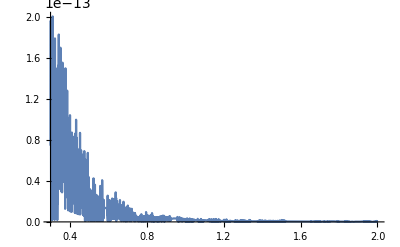

```mathematica
error =Abs[ Graf[BesselJ,20]/BesselJ[n,R[l]]]/.{x[l]-> 0,y[l]-> 0, x[j]-> 2,y[j]-> 0, y->0};
Plot[error/.{n->3},{x,0.3,2},PlotRange-> All]
```